```mathematica
<<MaTeX`
```

## Первое приближение

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -2 vQ, + 2 vQ}, MaxRecursion->12];
```

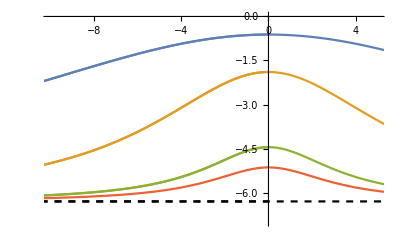

```mathematica
ϵ =4 10^-8;
image1 = Show[{
DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, 0, ϵ ν0 / 100}, 
PlotStyle->{, ,,{Black, Dashed}}, PlotRange->{{-10, 5}, {-7, 0}}, Filling->None
, PlotLegends->{MaTeX@"s=100",MaTeX@"s=10",MaTeX@"s=1",MaTeX@"s=0"},
Joined->True, AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"\\sim \\log {I_{\\mathrm{out}}}/{I_{\\mathrm{in}}}"}]
, DiscretePlot[
{-f1[100, ν0+ν], -f1[10, ν0+ν], -f1[1, ν0+ν], -f1[1/2, ν0+ν], -f1[0, ν0+ν]}, {ν,- ϵ ν0, + ϵ ν0, ϵ ν0 / 100}, 
Filling->None, Joined->True, PlotStyle->{, ,,,{Black, Dashed}}]
}]
```

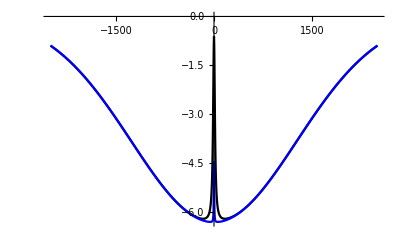

```mathematica
ϵ =8 10^-6;
image2 = DiscretePlot[
{-f1[100, ν0+ν], -f1[1, ν0+ν]}, {ν,- 0.7ϵ ν0, +0.7ϵ ν0, ϵ ν0 / 1000}, PlotRange->{Full, {Full, 0}},Filling->None, Joined->True,
PlotStyle->{Black, Blue}, PlotLegends->{MaTeX@"s=100",MaTeX@"s=10"},
AxesLabel->{MaTeX@"\\nu,\ \\text{MHz}", MaTeX@"\\sim \\log {I_{\\mathrm{out}}}/{I_{\\mathrm{in}}}"}]
```

```mathematica
(*Export[NotebookDirectory[]<>"v2.png", image2]*)
```

## Оценка контрастности

Оценим параметр κ из отношения β = I_out / I_in в глубине доплеровского провала.

```mathematica
β = 1/6; (* β = Subscript[I, out] / Subscript[I, in] *)
κx = -Log[β]/f1[0, ν0] (* c/м *)
```

0.284285

```mathematica
ClearAll[GetK];
GetK[β_, s_] :=  (β^(f1[s, ν0]/f1[0, ν0])-β)/(1-β);
```

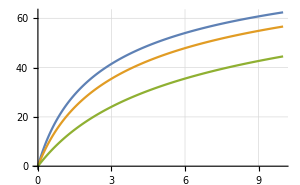

```mathematica
im3 = DiscretePlot[{100GetK[0.5, s], 100GetK[0.3, s], 100GetK[0.1, s]}, {s, 0, 10, 0.01}, Joined->True, Filling->None, (*PlotLabel->"Зависимость контрастности от параметра насыщения", *)(*PlotStyle->{RGBColor[0.,0.57,0.], Thickness[10^-2]}, *)GridLines->Automatic, AxesLabel->{MaTeX["s"], MaTeX["K,\\, \\%"]}, ImageSize->{300,150}, PlotLegends->{MaTeX["\\beta = 0.5"], MaTeX["\\beta = 0.3"], MaTeX["\\beta = 0.1"]}]
```

```mathematica
Export[NotebookDirectory[]<>"K.pdf", im3]
```

D:\Kami\git_folder\notes_5sem\rqc\saturation_spectr_simulation\K.pdf

-Graphics-